```mathematica
ClearAll[r,r0,u]
```

```mathematica
sol = DSolve[{D[r[x,t],t] + u*D[r[x,t],x]==0, r[x,0]==r0[x]}, r[x,t], {x,t}]
```

{{r[x,t]→r0[-u (t-x/u)]}}

```mathematica
sol[[1]]
```

{r[x,t]→r0[-t+x]}

```mathematica
u=1;
r0[x_]:=E^(-x^2);
r =r/.DSolve[{D[r[x,t],t] + u*D[r[x,t],x]==0, r[x,0]==r0[x]}, r, {x,t}] // Flatten//First
```

Function[{x,t},ⅇ^(-(-t+x)^2)]

```mathematica
u=1;
r0[x_]:=Exp[-x^2];

sol=DSolve[{D[r[x,t],t]+u*D[r[x,t],x]==0,r[x,0]==r0[x]},r,{x,t}]//First;

r[x_,t_]:=(r[x,t]/. sol)
```

DSolve::deqn: Equation or list of equations expected instead of True in the first argument {True,True}.

SetDelayed::write: Tag Function in Function[{x,t},ⅇ^(-(-t+x)^2)][x_,t_] is Protected.

$Failed

```mathematica
Plot3D[r[x,t], {x,-2,10}, {t,0,10}, AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
Manipulate[Plot[r[x,t], {x, -2,10}, PlotRange->{Automatic, {0,1}}], {t,0,10}]
```

```mathematica
ContourPlot[r[x,t],{x, -2, 10}, {t, 0, 10}, PlotLegends->Automatic]
```

```mathematica
ClearAll[r,r0,u]
```

```mathematica
sol1 = DSolve[{D[u[x,t],t]==d*D[u[x,t],{x,2}], u[x,0]==u0[x]}, u[x,t],{x,t}]
```

{{u[x,t]→(ⅇ^(ⅈ x K[1]-d t K[1]^2) ⅇ^(-ⅈ x K[1]) u0[x]x-∞∞K[1]-∞∞)/(2 π)}}

```mathematica
d=0.1;
u0[x_]:=Exp[-x^2];
DSolve[{D[u[x,t],t]==d1*D[u[x,t],{x,2}], u[x,0]==u0[x]}, u,{x,t}]
```

{{u→Function[{x,t},ConditionalExpression[(ⅇ^(-x^2/(1+4 d1 t)))/(√(1+4 d1 t)), t Re[d1]>-1/4]]}}

```mathematica
d=0.1;
u0[x_]:=Exp[-x^2];

sol=NDSolve[{Derivative[0,1][u][x,t]==d*Derivative[2,0][u][x,t],u[x,0]==u0[x],u[-5,t]==0,u[5,t]==0},u,{x,-5,5},{t,0,2}];

Plot3D[Evaluate[u[x,t]/. sol],{x,-5,5},{t,0,2},AxesLabel->{"x","t","u"}]
```

-Graphics3D-

```mathematica
Manipulate[Plot[Evaluate[u[x,t]/. sol],{x,-5,5},PlotRange->{Automatic, {0,1}}],{t,0.0001,2}]
```

InterpolatingFunction::dmval: Input value {-4.9998,0.0001} lies outside the range of data in the interpolating function. Extrapolation will be used.

ReplaceAll::reps: 
   {sol} is neither a list of replacement rules nor a valid dispatch table,
     and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps
     will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {-4.9998,0.0001} lies outside the range of data in the interpolating function. Extrapolation will be used.

ReplaceAll::reps: {True,True} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {True,True} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

```mathematica
ContourPlot[Evaluate[u[x,t]/. sol],{x,-5,5},{t,0.0001,2}]
```

```mathematica
d=0.1;
u0[x_]:=Exp[-x^2];
uAnalytic[x_,t_]:=N[1/Sqrt[4 Pi d t]*Exp[-x^2/(4 d t)],50];
sol=NDSolve[{Derivative[0,1][u][x,t]==d*Derivative[2,0][u][x,t],u[x,0]==u0[x],u[-5,t]==0.001,u[5,t]==0},u,{x,-5,5},{t,0.001,2}];
Manipulate[Plot[{uAnalytic[x,t],Evaluate[u[x,t]/. sol]},{x,-5,5},PlotRange->{Automatic,{0,1}},PlotLegends->{"Analytical","NDSolve"}],{t,0.001,2}]
```

NDSolve::ibcinc: Warning: boundary and initial conditions are inconsistent.

General::munfl: Exp[-62494.9] is too small to represent as a normalized machine number; precision may be lost.

ReplaceAll::reps: {True,True} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {True,True} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {True,True} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {sol} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {sol} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {sol} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {sol} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

```mathematica
Clear[ut, ut0]
```

```mathematica
solsecond = DSolve[{D[ut[t,x], {t,2}]==c^2*D[ut[t,x], {x,2}], ut[0,x]==ut0[x],Derivative[1,0][ut][0,x]==0}, ut[t,x], {t,x}]
```

```mathematica
{{ut[t,x]->Piecewise[{{1/2 (ut0[-t+x]+ut0[t+x]), t≥0}, {Indeterminate, True}}]}}
```

{{ut[t,x]→Piecewise[{{1/2 (ut0[-t+x]+ut0[t+x]), t≥0}, {Indeterminate, True}}]}}

```mathematica
c=1;
ut0[x_]:=Exp[-x^2];
anatitut[t_, x_]= ut[t,x]/.solsecond[[1]]
```

Piecewise[{{1/2 (ⅇ^(-(-t+x)^2)+ⅇ^(-(t+x)^2)), t≥0}, {Indeterminate, True}}]

```mathematica
Plot3D[ut[t,x],{t,0,6},{x,-10,10}]
```

-Graphics3D-

```mathematica
ut1[x_]:=0;
ut0[x_]:=Exp[-x^2];
solsecondn = NDSolve[{D[ut[t,x], {t,2}]==c^2*D[ut[t,x], {x,2}], ut[0,x]==ut0[x],Derivative[1,0][ut][0,x]==ut1[x], ut[t, -10]==0, ut[t,10]==0}, ut, {t, 0, 6}, {x,-10, 10}]
```

{{ut→InterpolatingFunction[…]}}

```mathematica
Plot3D[Evaluate[ut[t,x]/. solsecondn],{t,0,5},{x,-10,10},PlotRange->All]
```

-Graphics3D-

```mathematica
ContourPlot[Evaluate[ut[t,x]/. solsecondn],{t,0,5},{x,-10,10},PlotRange->All]
```

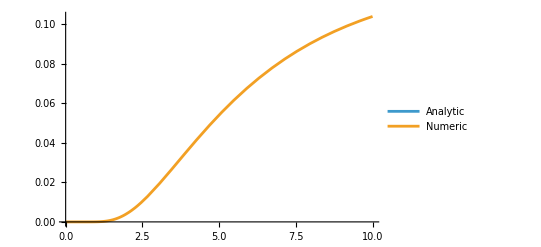

```mathematica
t0=2;

Plot[{un[t0,x]/. solsecondn[[1]], uAnalytic[t0,x]},{x,-10,10},PlotLegends->{"Analytic","Numeric"},PlotRange->All]
```

```mathematica
Manipulate[Plot[{un[t,x]/. solsecondn[[1]],uAnalytic[t,x]},{x,-10,10},PlotRange->{0,1},PlotLegends->{"Analytic","Numeric"}],{t,0,3}]
```

ReplaceAll::reps: {solsecondn⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {solsecondn⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {solsecondn⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {solsecondn⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {solsecondn⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {solsecondn⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {solsecondn⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {solsecondn⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {solsecondn⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

```mathematica
Plot[uAnalytic[t,x]-(un[t,x]/. solsecondn[[1]]),{x,-10,10},PlotRange->All]
```

```mathematica
MaxValue[Abs[uAnalytic[t,x]-(un[t,x]/. solsecondn[[1]])],{x,-10,10}]
```

MaxValue::ivar: -10 is not a valid variable.

MaxValue[Abs[(0.892062 2.7182818284590452353602874713526624977572470937^(-(2.5 t^2)/x))/(√x)-un[t,x]],{x,-10,10}]

```mathematica
(*Параметры*)a=1.0;              (*скорость переноса*)
xMin=-10;xMax=10;
h=0.1;              (*шаг по пространству*)
tau=0.05;           (*шаг по времени*)
tMax=6.0;

xGrid=Range[xMin,xMax,h];
nx=Length[xGrid];
nt=Ceiling[tMax/tau]+1;
timeGrid=Table[(n-1)*tau,{n,1,nt}];

(*Начальное условие:ступенька или гаусс*)
phi[x_]:=Exp[-(x+2)^2/0.5]         (*гаусс*)
(*phi[x_]:=1/(1+Exp[-(x)])          (*ступенька*)*)

(*Источник σ(x,t)—можно менять*)
sigma[x_,t_]:=0.5*Exp[-x^2/8]*Cos[0.8 t]  (*пример:локализованный в x,завиcит от t*)
(*sigma[x_,t_]:=0.5;                  (*постоянный рост*)*)
```

```mathematica
ExplicitUpwind[a_,h_,tau_,xGrid_,timeGrid_,phi_,sigma_]:=Module[{nx=Length[xGrid],nt=Length[timeGrid],u,lambda},u=ConstantArray[0.,{nt,nx}];
(*начальное условие*)u[[1,All]]=phi/@xGrid;
lambda=a tau/h;
Do[(*граничные условия:перенесём значение слева (простая фиксация)*)Do[(*upwind для a>0:u_i^{n+1}=u_i^n-λ (u_i^n-u_{i-1}^n)+tau*sigma_i^n*u_i^n*)If[i==1,(*левый край:используем транспонированное значение (или фиксируем 0)*)u[[n+1,i]]=u[[n,i]]-lambda (u[[n,i]]-0.)+tau*sigma[xGrid[[i]],timeGrid[[n]]]*u[[n,i]],u[[n+1,i]]=u[[n,i]]-lambda (u[[n,i]]-u[[n,i-1]])+tau*sigma[xGrid[[i]],timeGrid[[n]]]*u[[n,i]]],{i,1,nx}],{n,1,nt-1}];
u];

uExp=ExplicitUpwind[a,h,tau,xGrid,timeGrid,phi,sigma];
```

```mathematica
ImplicitBackwardEuler[a_,h_,tau_,xGrid_,timeGrid_,phi_,sigma_]:=Module[{nx=Length[xGrid],nt=Length[timeGrid],u,lambda,A,b,i},u=ConstantArray[0.,{nt,nx}];
u[[1,All]]=phi/@xGrid;
lambda=a tau/h;
(*Матрица системы для шага n->n+1:для a>0 и backward-upwind:u_i^{n+1}+λ(u_i^{n+1}-u_{i-1}^{n+1})-tau*sigma_i^{n+1} u_i^{n+1}=u_i^n=>(1+λ-tau*σ_i^{n+1}) u_i^{n+1}-λ u_{i-1}^{n+1}=u_i^n трёхдиаг:диагональ и нижняя диагональ (верхняя нулевая для upwind backward)*)Do[(*формируем A и b для текущего шага*)b=u[[n,All]];
A=SparseArray[{Band[{1,1}]->Table[1+lambda-tau*sigma[xGrid[[i]],timeGrid[[n+1]]],{i,nx}],Band[{2,1}]->Table[-lambda,{i,nx-1}]  (*нижняя диагональ:-λ*)},{nx,nx}];
(*граничные условия:для i=1 предполагаем значение от границы 0 (можно менять)*)(*можно также модифицировать первый уравнение,если задаём вх.поток*)b[[1]]-=0.*(-lambda);(*если хотим учесть граничную вкладку—сейчас 0*)(*решаем систему*)u[[n+1,All]]=LinearSolve[A,b];,{n,1,nt-1}];
u];

uImp=ImplicitBackwardEuler[a,h,tau,xGrid,timeGrid,phi,sigma];
```

```mathematica
CrankNicolson[a_,h_,tau_,xGrid_,timeGrid_,phi_,sigma_]:=Module[{nx=Length[xGrid],nt=Length[timeGrid],u,lambda,A,B,RHS},u=ConstantArray[0.,{nt,nx}];
u[[1,All]]=phi/@xGrid;
lambda=a tau/h;
Do[(*Схема (CN) для upwind-термов:(u^{n+1}-u^n)/tau+a*upwind((u^{n+1}+u^n)/2)/h=σ^{avg} (u^{n+1}+u^n)/2*)(*Это даёт трёхдиагональную систему;для простоты применим матричную форму:A u^{n+1}=B u^n*)A=SparseArray[{Band[{1,1}]->Table[1+(lambda/2)-(tau/2)*sigma[xGrid[[i]],timeGrid[[n+1]]],{i,nx}],Band[{2,1}]->Table[-(lambda/2),{i,nx-1}]},{nx,nx}];
B=SparseArray[{Band[{1,1}]->Table[1-(lambda/2)+(tau/2)*sigma[xGrid[[i]],timeGrid[[n]]],{i,nx}],Band[{2,1}]->Table[(lambda/2),{i,nx-1}]},{nx,nx}];
RHS=B.u[[n,All]];
u[[n+1,All]]=LinearSolve[A,RHS];,{n,1,nt-1}];
u];

uCN=CrankNicolson[a,h,tau,xGrid,timeGrid,phi,sigma];
```

-Graphics3D-

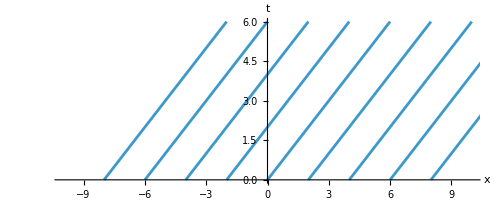

```mathematica
(*Вспомогательная функция:перевод матрицы в формат для ListPlot3D*)ListPlot3DFromMatrix[u_,xGrid_,timeGrid_]:=Module[{pts},pts=Flatten[Table[{xGrid[[i]],timeGrid[[n]],u[[n,i]]},{n,1,Length[timeGrid]},{i,1,Length[xGrid]}],1];
ListPlot3D[pts,AxesLabel->{"x","t","u"},Mesh->None,BoxRatios->{1,0.6,0.5}]];

(*3D:явная*)
ListPlot3DFromMatrix[uExp,xGrid,timeGrid]
(*3D:неявная*)
(*ListPlot3DFromMatrix[uImp,xGrid,timeGrid]*)

(*ContourPlot (плотность)*)
ArrayPlot[Transpose[uExp],DataReversed->True,FrameLabel->{"t","x"}]
(*Или более гладко:DensityPlot с интерполяцией*)
(*можно создать интерполяционную функцию и потом ContourPlot*)

(*Характеристики:прямые x=x0+a t от набора начальных точек*)
charLines=Table[ParametricPlot[{x0+a s,s},{s,0,tMax},PlotRange->{{xMin,xMax},{0,tMax}}],{x0,Range[-8,8,2]}];
Show[charLines,AxesLabel->{"x","t"}]
```

```mathematica
(*Создадим интерполяцию для удобства*)uExpInterp=ListInterpolation[uExp,{timeGrid,xGrid}];
uImpInterp=ListInterpolation[uImp,{timeGrid,xGrid}];

Manipulate[Plot[{uExpInterp[t,x],uImpInterp[t,x]},{x,xMin,xMax},PlotRange->All,PlotLegends->{"Explicit","Implicit"},AxesLabel->{"x","u"}],{t,0,tMax}]
```

InterpolatingFunction::dmval: Input value {6.,-4.9998} lies outside the range of data in the interpolating function. Extrapolation will be used.

```mathematica
ListPlot3D[uExp,Mesh->None,AxesLabel->{"i (space index)","n (time index)","u"},PlotRange->All,BoxRatios->{1,1,0.6}]
```

-Graphics3D-

```mathematica
ListPlot3D[uImp,Mesh->None,AxesLabel->{"i","n","u"},PlotRange->All,BoxRatios->{1,1,0.6}]
```

-Graphics3D-

```mathematica
Manipulate[ListLinePlot[uExp[[n,All]],PlotRange->All,AxesLabel->{"i","u"},PlotLabel->("Explicit scheme — time level n = "<>ToString[n])],{n,1,nt,1}]
```

```mathematica
(*uExp,uImp,uCN уже вычислены ранее*)uExpInterp=ListInterpolation[uExp,{timeGrid,xGrid}];
uImpInterp=ListInterpolation[uImp,{timeGrid,xGrid}];
uCNInterp=ListInterpolation[uCN,{timeGrid,xGrid}];

(*Если есть аналитика для σ=σ(t)*)
uAnalyticFunc[x_,t_]:=phi[x-a t]*Exp[Integrate[sigma[x-a s,s],{s,0,t}]];
(*Можно заменить на численное интегрирование для произвольного σ*)
```

```mathematica
Manipulate[Plot[Switch[scheme,"Explicit",uExpInterp[t,x],"Implicit",uImpInterp[t,x],"Crank–Nicolson",uCNInterp[t,x],"Analytic",uAnalyticFunc[x,t]],{x,xMin,xMax},PlotRange->All,AxesLabel->{"x","u"},PlotLabel->"Scheme: "<>scheme<>", t = "<>ToString[NumberForm[t,{3,2}]]],{{t,0},0,tMax},{{scheme,"Explicit"},{"Explicit","Implicit","Crank–Nicolson","Analytic"}}]
```

```mathematica
ContourPlot[Evaluate[Switch[scheme,"Explicit",uExpInterp[t,x],"Implicit",uImpInterp[t,x],"Crank–Nicolson",uCNInterp[t,x],"Analytic",uAnalyticFunc[x,t]]],{t,0,tMax},{x,xMin,xMax},PlotRange->All,FrameLabel->{"t","x"},ColorFunction->"Rainbow",Contours->20]
```

-Graphics-

```mathematica
(*Параметры*)a=1.0;
xMin=-5;xMax=5;
h=0.1;tau=0.05;tMax=4;
xGrid=Range[xMin,xMax,h];
timeGrid=Range[0,tMax,tau];
nx=Length[xGrid];nt=Length[timeGrid];

(*Начальное условие*)
u0[x_]:=Exp[-x^2];

(*Источник*)
sigma[x_,t_]:=0.5*Exp[-x^2/4];  (*пример:локализованный рост*)
```

```mathematica
uAnalytic[x_,t_]:=u0[x-a t] Exp[NIntegrate[sigma[x-a (t-s),s],{s,0,t}]]
```

```mathematica
uExp=ConstantArray[0.,{nt,nx}];
uExp[[1]]=u0/@xGrid;
lambda=a*tau/h;

Do[Do[If[i==1,uExp[[n+1,i]]=uExp[[n,i]]+tau*sigma[xGrid[[i]],timeGrid[[n]]]*uExp[[n,i]],uExp[[n+1,i]]=uExp[[n,i]]-lambda*(uExp[[n,i]]-uExp[[n,i-1]])+tau*sigma[xGrid[[i]],timeGrid[[n]]]*uExp[[n,i]]],{i,1,nx}],{n,1,nt-1}];
uExpInterp=ListInterpolation[uExp,{timeGrid,xGrid}];
```

```mathematica
uImp=ConstantArray[0.,{nt,nx}];
uImp[[1]]=u0/@xGrid;
lambda=a*tau/h;

Do[(*коэффициенты для матрицы A*)diag=Table[1+lambda-tau*sigma[xGrid[[i]],timeGrid[[n+1]]],{i,nx}];
subdiag=Table[-lambda,{nx-1}];
(*матрица системы*)A=SparseArray[{Band[{1,1}]->diag,Band[{2,1}]->subdiag},{nx,nx}];
(*правая часть*)b=uImp[[n,All]];
(*решение на следующий шаг*)uImp[[n+1,All]]=LinearSolve[A,b];,{n,1,nt-1}];

(*интерполяция для удобного обращения*)
uImpInterp=ListInterpolation[uImp,{timeGrid,xGrid}];
```

```mathematica
uCN=ConstantArray[0.,{nt,nx}];
uCN[[1]]=u0/@xGrid;

Do[(*коэффициенты для матриц*)diagA=Table[1+lambda/2-tau/2*sigma[xGrid[[i]],timeGrid[[n+1]]],{i,nx}];
subdiagA=Table[-lambda/2,{nx-1}];
diagB=Table[1-lambda/2+tau/2*sigma[xGrid[[i]],timeGrid[[n]]],{i,nx}];
subdiagB=Table[lambda/2,{nx-1}];
A=SparseArray[{Band[{1,1}]->diagA,Band[{2,1}]->subdiagA},{nx,nx}];
B=SparseArray[{Band[{1,1}]->diagB,Band[{2,1}]->subdiagB},{nx,nx}];
b=B.uCN[[n,All]];
uCN[[n+1,All]]=LinearSolve[A,b];,{n,1,nt-1}];

uCNInterp=ListInterpolation[uCN,{timeGrid,xGrid}];
```

```mathematica
Manipulate[Plot[{uAnalyticInterp[t,x],uExpInterp[t,x],uImpInterp[t,x],uCNInterp[t,x]},{x,xMin,xMax},PlotRange->All,PlotStyle->{Red,Blue,Green,Orange},PlotLegends->{"Analytic","Explicit","Implicit","Crank–Nicolson"},AxesLabel->{"x","u"},PlotLabel->"Comparison of schemes at t = "<>ToString[NumberForm[t,{3,2}]]]
 ,{t,0,tMax}
]
```

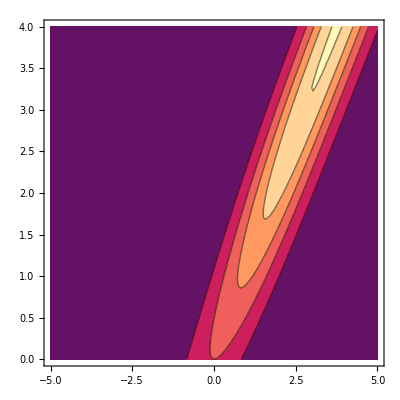

```mathematica
ContourPlot[uAnalytic[x,t],{x,xMin,xMax},{t,0,tMax},PlotRange->All]
```

```mathematica
Plot3D[uAnalytic[x,t],{x,xMin,xMax},{t,0,tMax},PlotRange->All]
```

-Graphics3D-